# Abstract Tile Assembly Model (aTAM) simulator

This notebook was prepared by Erik Winfree <winfree@caltech.edu> for Caltech BE/CS 191a, Winter 2022.  
Do not share this with anyone who is not currently taking the class unless you have permission from Erik Winfree.

This simulator is simple and flexible, but slow.  For 1000x faster simulation, check out “xgrow” or “ISU TAM”.

To review, the aTAM model simulates growth from a seed tile or seed assembly under the assumptions that all tile types are at the same concentration that remains constant over time, that each tile collides with each available site at an equal rate but only those the bind strongly enough will stick.  Specifically, at each stochastic step, one uniformly random choice of (site, tile type) is chosen from among all the valid option for new tiles that will stick.

A tile will be generically 
	Tile[ID, {north bond type, east, south, west}, color]
	
A bond strength function must be defined on pairs of bonds, e.g.
	G[x_,y_] := value
	
An assembly will be a matrix where each element is either a tile ID or the symbol “empty”, followed by the (x,y) coordinate of the upper-left cell.
	TileAssembly[ { {empty or a tile,...},...},{x,y} ]
	
A tile system will be generically
	TileSystem[set of tiles, binding threshold, bond type strength function]

To explore the simulator and learn how to use it, it will probably be effective to skip the “initialization cells” (grey) that provide key function definitions, and to just go to the examples and execute them.  In addition to executing them, it’s worth examining the data structures and understanding how they are being used, by trying different examples and by using “// InputForm” to see the full representation.

```mathematica
(* Pulls out the detailed information about a tile from its symbolic ID name. *)
(* This would be done more efficiently with an association, but it only used to build the seed, so not critical. *)
FullTile[ID_,tileset_]:=With[{matches=Select[tileset,(First[#]===ID)&]},
If[Length[matches]==1,First[matches],Error]]
```

```mathematica
(* Builds a tile assembly with detailed information, based on a 2D array of tile ID names. *)
SeedAssembly[MIDs_,tileset_List]:=TileAssembly[Map[FullTile[#,tileset]&,MIDs,{2}],{0,0}] 
SeedAssembly[MIDs_,tilesystem_TileSystem]:=SeedAssembly[MIDs,First[TileSystem]]
```

```mathematica
(* This makes sure that there is a two-row / two-column buffer of "empty" around the assembly. *)
Clear[PadAssembly]
PadAssembly[TileAssembly[M_,{di_,dj_}]]:=PadAssembly[TileAssembly[Join[{Table[empty,Length[First[M]]]},M],{di-1,dj}]]/;Union[M[[1,;;]]]=!={empty}
PadAssembly[TileAssembly[M_,{di_,dj_}]]:=PadAssembly[TileAssembly[Join[M,{Table[empty,Length[First[M]]]}],{di,dj}]]/;Union[M[[-1,;;]]]=!={empty}
PadAssembly[TileAssembly[M_,{di_,dj_}]]:=PadAssembly[TileAssembly[Join[{empty},#]&/@M,{di,dj-1}]]/;Union[M[[;;,1]]]=!={empty}
PadAssembly[TileAssembly[M_,{di_,dj_}]]:=PadAssembly[TileAssembly[Join[#,{empty}]&/@M,{di,dj}]]/;Union[M[[;;,-1]]]=!={empty}
PadAssembly[TileAssembly[M_,{di_,dj_}]]:=PadAssembly[TileAssembly[Join[{Table[empty,Length[First[M]]]},M],{di-1,dj}]]/;Union[M[[2,;;]]]=!={empty}
PadAssembly[TileAssembly[M_,{di_,dj_}]]:=PadAssembly[TileAssembly[Join[M,{Table[empty,Length[First[M]]]}],{di,dj}]]/;Union[M[[-2,;;]]]=!={empty}
PadAssembly[TileAssembly[M_,{di_,dj_}]]:=PadAssembly[TileAssembly[Join[{empty},#]&/@M,{di,dj-1}]]/;Union[M[[;;,2]]]=!={empty}
PadAssembly[TileAssembly[M_,{di_,dj_}]]:=PadAssembly[TileAssembly[Join[#,{empty}]&/@M,{di,dj}]]/;Union[M[[;;,-2]]]=!={empty}
PadAssembly[TA_TileAssembly]:=TA

(* With min and max coordinates specified, places the assembly in an otherwise empty field spanning these coords. *)

PadAssembly[TileAssembly[M_,{di_,dj_}],{{mini_,minj_},{maxi_,maxj_}}]:=
If[mini≤di&&di+Length[M]-1≤maxi && minj≤dj&&dj+Length[First[M]]-1≤maxj,
Module[{ni=maxi-mini+1,nj=maxj-minj+1,newM},
newM=Table[empty,ni,nj];
newM[[di-mini+Range[Length[M]],dj-minj+Range[Length[First[M]]]]]=M;
TileAssembly[newM,{mini,minj}]
],
Error
]
```

```mathematica
PaddedAssemblyQ[TileAssembly[M_,_]]:=Union[Join[M[[1,;;]],M[[-1,;;]],M[[;;,1]],M[[;;,-1]]]]==={empty}
```

```mathematica
AssemblyEmptyQ[TileAssembly[M_,{di_,dj_}],{i_,j_}]:=M[[i-di+1,j-dj+1]]===empty
```

```mathematica
BindingEnergy[TileAssembly[M_,{di_,dj_}],Tile[_,{n_,e_,s_,w_},_],{i_,j_},G_]:=
(If[M[[i-1-di+1,j-dj+1]]===empty,0,G[M[[i-1-di+1,j-dj+1]][[2,3]],n]]+
If[M[[i-di+1,j+1-dj+1]]===empty,0,G[M[[i-di+1,j+1-dj+1]][[2,4]],e]]+
If[M[[i+1-di+1,j-dj+1]]===empty,0,G[M[[i+1-di+1,j-dj+1]][[2,1]],s]]+
If[M[[i-di+1,j-1-dj+1]]===empty,0,G[M[[i-di+1,j-1-dj+1]][[2,2]],w]])
```

```mathematica
(* The upper-left site of the seed assembly grid is {i,j}={0,0}. *)
TileChoices[TileAssembly[M_,{di_,dj_}],{i_,j_},TileSystem[tileset_,T_,G_]]:=If[M[[i-di+1,j-dj+1]]=!=empty,{},
Select[tileset,BindingEnergy[TileAssembly[M,{di,dj}],#,{i,j},G]≥T&]]
```

```mathematica
AdditionOptions[TileAssembly[M_,{di_,dj_}],{i_,j_},TS_TileSystem]:=With[{imax=Length[M],jmax=Length[First[M]]},
{{i,j},#}&/@TileChoices[TileAssembly[M,{di,dj}],{i,j},TS]]
```

```mathematica
AllAdditionOptions[TileAssembly[M_,{di_,dj_}],TS_TileSystem]:=With[{imax=Length[M],jmax=Length[First[M]]},
Flatten[Table[
AdditionOptions[TileAssembly[M,{di,dj}],{i,j},TS],
{i,di+1,di+imax-2},{j,dj+1,dj+jmax-2}],2]]
```

```mathematica
LocalAdditionOptions[TileAssembly[M_,{di_,dj_}],{i_,j_},TS_TileSystem]:=With[{imax=Length[M],jmax=Length[First[M]]},
Flatten[Table[
AdditionOptions[TileAssembly[M,{di,dj}],{ni,nj},TS],
{ni,i-1,i+1},{nj,j-1,j+1}],2]]
```

```mathematica
AddTile[TA_TileAssembly,{{i_,j_},tile_}]:=Module[{M,di,dj},
M=First[TA]; {di,dj}=Last[TA];
M[[i-di+1,j-dj+1]]=tile;
PadAssembly[TileAssembly[M,{di,dj}]]
]
```

```mathematica
SimulateAssemblyWithOptions[TA_TileAssembly,TS_TileSystem, timeout_,precomputedoptions_]:= Module[{assem,steps=0,options,i,j,tile},
assem=PadAssembly[TA]; 
options=If[Length[precomputedoptions]==0,AllAdditionOptions[assem,TS],precomputedoptions];
While[options=!={} && steps<timeout,
steps++;
{{i,j},tile}=RandomChoice[options];
assem=AddTile[assem,{{i,j},tile}];
options=Select[Union[options,LocalAdditionOptions[assem,{i,j},TS]],AssemblyEmptyQ[assem,First[#]]&];
];
{assem,options}
]
SimulateAssembly[TA_TileAssembly,TS_TileSystem, timeout_:1000]:=First[SimulateAssemblyWithOptions[TA,TS,timeout,{}]]
```

```mathematica
TileGraphics[Tile[ID_,{n_,e_,s_,w_},color_]]:=Graphics[{EdgeForm[Thick],color,Rectangle[{0,0},{1,1}],
Text[Style[ToString[ID],Black,FontSize->Scaled[0.2]],{.5,.5}],
Rotate[Text[Style[ToString[n/.Null->""],Black,FontSize->Scaled[0.15]],{.5,.85}],0,{0.5,0.85}],
Rotate[Text[Style[ToString[e/.Null->""],Black,FontSize->Scaled[0.15]],{.85,.5}],-Pi/2,{.85,.5}],
Rotate[Text[Style[ToString[s/.Null->""],Black,FontSize->Scaled[0.15]],{.5,.15}],-Pi,{.5,.15}],
Rotate[Text[Style[ToString[w/.Null->""],Black,FontSize->Scaled[0.15]],{.15,.5}],Pi/2,{.15,.5}]
}]
Format[tile:Tile[ID_,{n_,e_,s_,w_},color_]]:=TileGraphics[tile]
```

```mathematica
AssemblyGraphics[TileAssembly[M_,_]]:=ArrayPlot[M,ColorRules->{empty->White,Tile[_,_,color_]:>color}]
Format[assembly:TileAssembly[M_,_]]:=AssemblyGraphics[assembly]
```

```mathematica
DetailForm[TileAssembly[M_,_]]:=With[{newM=M/.empty->Tile["",{Null,Null,Null,Null},White],n=Length[M],m=Length[First[M]],gap=0.07},
Graphics[Table[Translate[List@@TileGraphics[newM[[i,j]]],(1+gap)*{j,-i}]/.Scaled[f_]:>Scaled[f/m/(1+gap)],{i,1,n},{j,1,m}]]]
```

```mathematica
Format[TileSystem[tileset_,T_,G_]]:="TileSystem[tiles...,T="<>ToString[T]<>", G]"
```

```mathematica
SimulateAssemblyHistory[TA_TileAssembly,TS_TileSystem, timeout_:1000]:= Module[{assem,steps=0,options,i,j,tile, history},
assem=PadAssembly[TA]; options=AllAdditionOptions[assem,TS]; history={};
While[options=!={} && steps<timeout,
steps++;
{{i,j},tile}=RandomChoice[options];
AppendTo[history,{{i,j},tile}];
assem=AddTile[assem,{{i,j},tile}];
options=Select[Union[options,LocalAdditionOptions[assem,{i,j},TS]],AssemblyEmptyQ[assem,First[#]]&];
];
{TA,history}
]
```

```mathematica
AnimateAssemblyHistory[{seed_TileAssembly,history_},maxframes_:1000]:=Module[{assem,frames,steps,mini,maxi,minj,maxj},
mini=Min[First[First[#]]&/@history];maxi=Max[First[First[#]]&/@history];
minj=Min[Last[First[#]]&/@history];maxj=Max[Last[First[#]]&/@history];
assem=PadAssembly[seed,{{mini-2,minj-2},{maxi+2,maxj+2}}];frames={assem};steps=Length[history];
For[s=1,s≤steps,s++,
assem=AddTile[assem,history[[s]]];
If[s/steps ≥ Length[frames]/Min[maxframes,steps],AppendTo[frames,assem]]];
Animate[frames[[t]],{t,1,Length[frames],1},AnimationRepetitions->1,DefaultDuration->10]
]
```

```mathematica
ClearAll[SimulatePuncturedAssemblyHistory]
Options[SimulatePuncturedAssemblyHistory]={BlastRate->0.01,BlastSize->5, PreserveSeed->True,PreserveBoundary->2,KeepHistory->True,GrowthOptions->None};
SimulatePuncturedAssemblyHistory[TA_TileAssembly,TS_TileSystem, timeout_:1000,OptionsPattern[]]:= Module[{assem,steps=0,options,i,j,tile, keep,history,di,dj,seedi,seedj,i1,i2,j1,j2,mi,mj,blastrate,blastsize,preserveseed,boundary},
blastrate=OptionValue[BlastRate];blastsize=OptionValue[BlastSize];preserveseed=OptionValue[PreserveSeed];
boundary=OptionValue[PreserveBoundary];
assem=PadAssembly[TA]; 
options=If[OptionValue[GrowthOptions]===None||OptionValue[GrowthOptions]==={},AllAdditionOptions[assem,TS],OptionValue[GrowthOptions]]; 
history={};keep=OptionValue[KeepHistory];
While[options=!={} && steps<timeout,
steps++;
{di,dj}=Last[assem];{mi,mj}={Length[First[assem]],Length[First[First[assem]]]};{seedi,seedj}={0,0};
If[RandomReal[]<blastrate && mi>2boundary+blastsize && mj > 2boundary+blastsize, 
(* blast: remove a random rectangular patch, so long as it doesn't include the seed *)
i1=RandomInteger[mi-2boundary-blastsize]+boundary+di; 
j1=RandomInteger[mj-2boundary-blastsize]+boundary+dj; 
{i2,j2}={i1+blastsize-1,j1+blastsize-1};
(* Print["Assem ",{di,dj}," to ",{di+mi-1,dj+mj-1}," i.e. ",{mi,mj}," : ",{i1,j1}," to ",{i2,j2}]; *)
If[!preserveseed || !(i1≤seedi≤i2 && j1≤seedj≤j2),
Do[
If[!AssemblyEmptyQ[assem,{i,j}],
assem=AddTile[assem,{{i,j},empty}];
If[keep,AppendTo[history,{{i,j},empty}]]
],
{i,i1,i2},{j,j1,j2}];
(* Print["done erasing"]; *)
options=Cases[options,{{i_,j_},tile_} /; i<i1-1 || i>i2+1 || j<j1-1 || j>j2+1];
(* Print["done clearing options"]; *)
options = Select[Union[options,
Flatten[Table[AdditionOptions[assem,{ni,nj},TS],
{ni,i1-1,i2+1},{nj,j1-1,j2+1}],2]],
AssemblyEmptyQ[assem,First[#]]&];
(* Print["done adding options"];*)
], 
(* growth: add a tile somewhere *)
{{i,j},tile}=RandomChoice[options];
If[keep,AppendTo[history,{{i,j},tile}]];
assem=AddTile[assem,{{i,j},tile}];
options=Select[Union[options,LocalAdditionOptions[assem,{i,j},TS]],AssemblyEmptyQ[assem,First[#]]&];
];
];
If[OptionValue[GrowthOptions]===None,
If[keep,{TA,history},{assem}],
If[keep,{TA,history,options},{assem,options}]]
]
```

## A simple test case: a small letter H

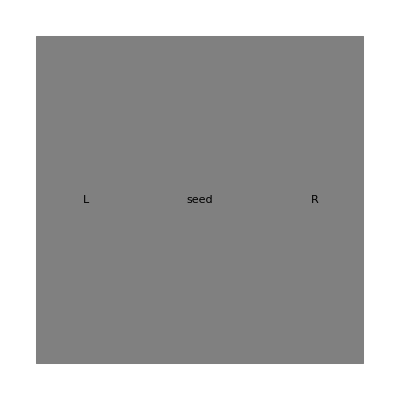
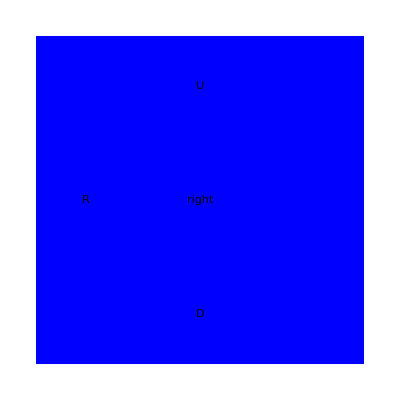
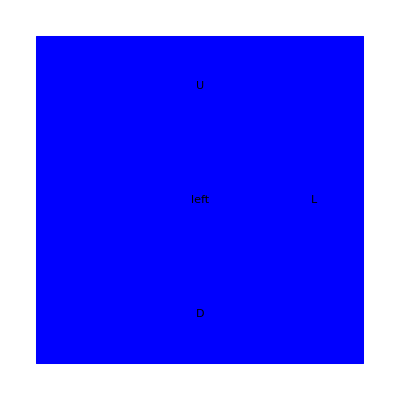
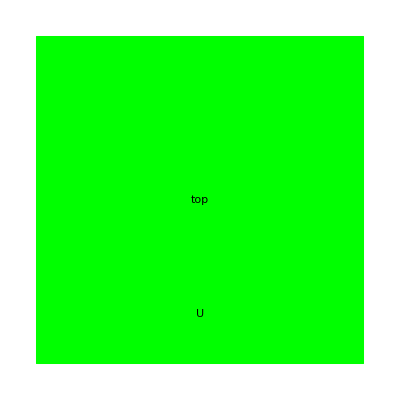
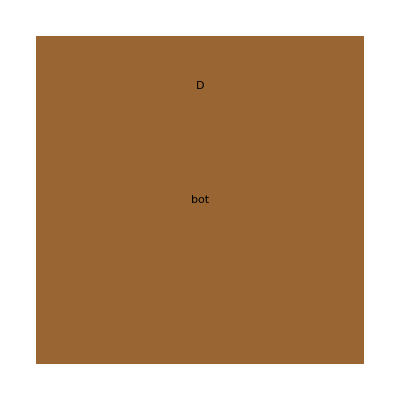

```mathematica
(* Define the tile set *)
LetterTiles={
Tile[seed,{Null,R,Null,L},Gray],
Tile[right,{U,Null,D,R},Blue],
Tile[left,{U,L,D,Null},Blue],
Tile[top,{Null,Null,U,Null},Green],
Tile[bot,{D,Null,Null,Null},Brown]
}
```

```mathematica
(* Define the bond strength function *)
Clear[LetterG]
LetterG[Null]=0;
LetterG[_]=1;
LetterG[x_,y_]:=If[x===y,LetterG[x],0]
```

```mathematica
(* Collect the tile set, threshold T, and bond strength function into one object *)
LetterTS=TileSystem[LetterTiles,1,LetterG];
```

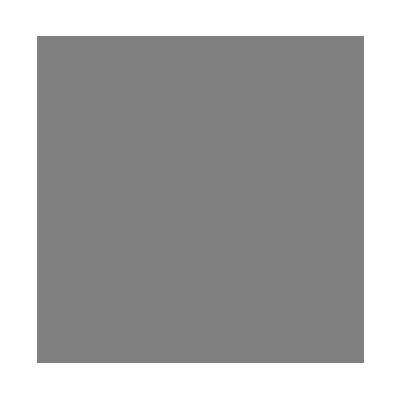

```mathematica
(* Build a TileAssembly object containing just the seed tile *)
LetterSeed=SeedAssembly[{{seed}},LetterTiles]
```

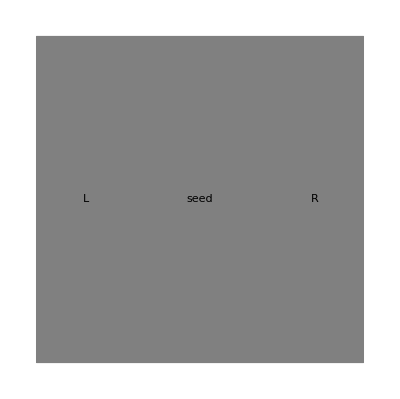

```mathematica
DetailForm[LetterSeed]
```

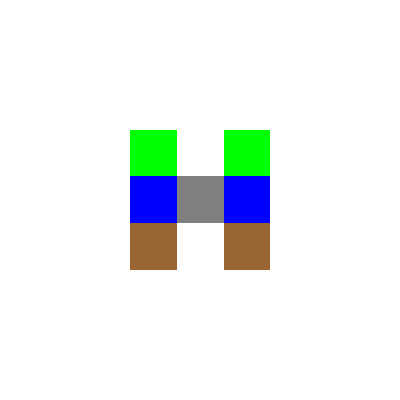

```mathematica
small=SimulateAssembly[LetterSeed,LetterTS,10]
```

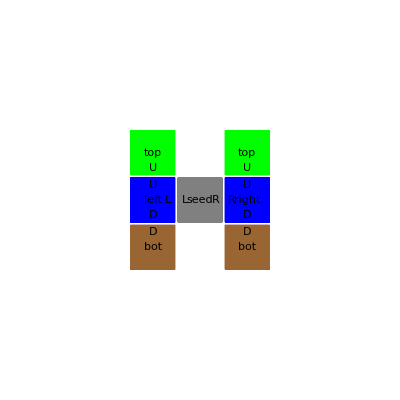

```mathematica
small//DetailForm
```

```mathematica
historyinfo=SimulateAssemblyHistory[LetterSeed,LetterTS,10];
```

```mathematica
AnimateAssemblyHistory[historyinfo]
```

## A simple test case: the Sierpinski tile set

```mathematica
(* Define the tile set *)
SierpinskiTiles={
Tile[seed,{B,B,Null,Null},Gray],
Tile[north,{B,1,B,Null},Blue],
Tile[east,{1,B,Null,B},Blue],
Tile[R00,{0,0,0,0},Green],
Tile[R01,{1,1,1,0},Red],
Tile[R10,{1,1,0,1},Red],
Tile[R11,{0,0,1,1},Green]
};
```

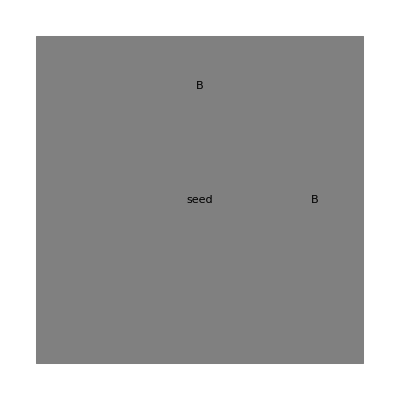
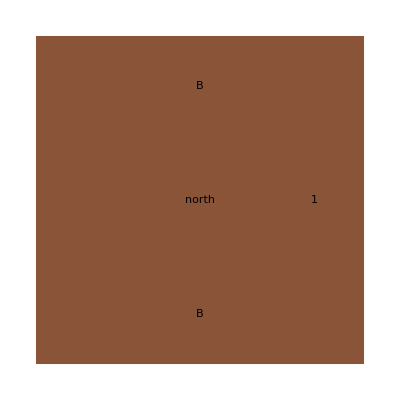
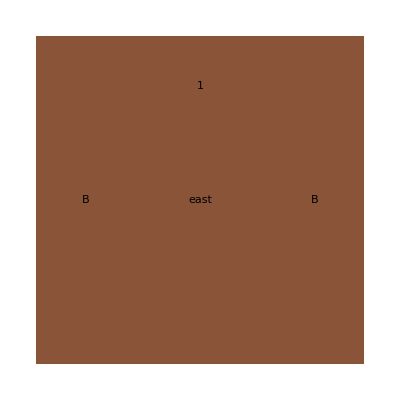
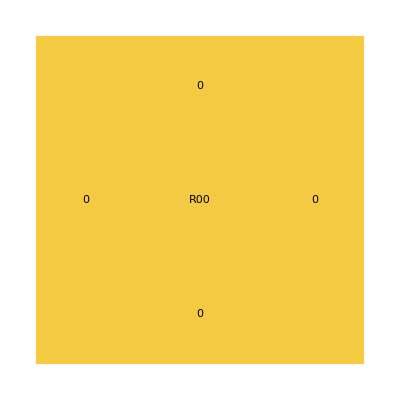
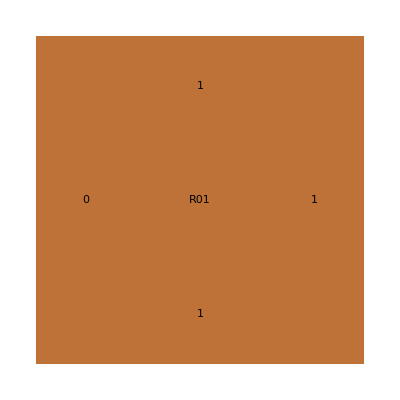
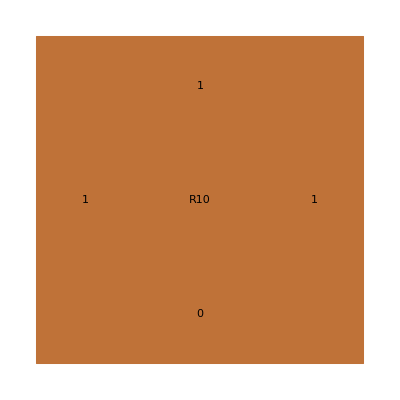
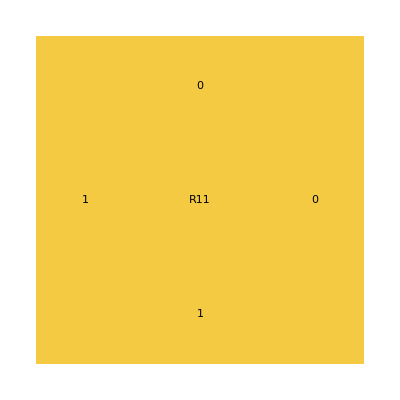

```mathematica
(* Make the colors more aesthetically pleasing... *)
SierpinskiTiles=SierpinskiTiles/.{
Blue->ColorData["FallColors"][0.45],
Red->ColorData["FallColors"][0.65],
Green->ColorData["FallColors"][1.0]
}
```

```mathematica
(* Define the bond strength function *)
Clear[SierpinskiG]
SierpinskiG[B]=2;
SierpinskiG[x_Integer]=1;
SierpinskiG[Null]=0;
SierpinskiG[x_,y_]:=If[x===y,SierpinskiG[x],0]
```

```mathematica
(* Collect the tile set, threshold T, and bond strength function into one object *)
SierpinskiTS=TileSystem[SierpinskiTiles,2,SierpinskiG];
```

```mathematica
(* Build a TileAssembly object containing just the seed tile *)
SierpinskiSeed=SeedAssembly[{{seed}},SierpinskiTiles];
```

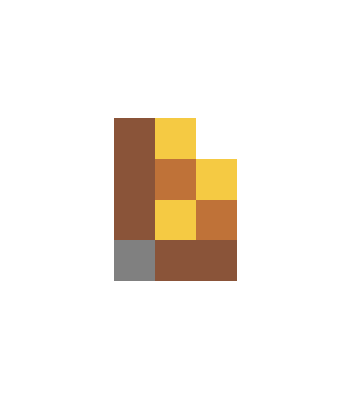

```mathematica
small=SimulateAssembly[SierpinskiSeed,SierpinskiTS,10]
```

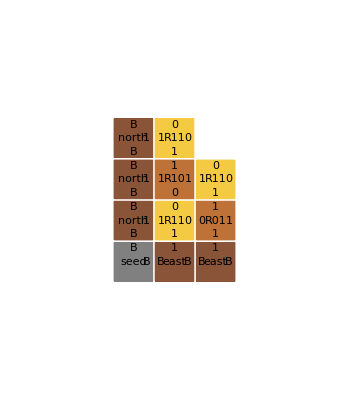

```mathematica
small//DetailForm
```

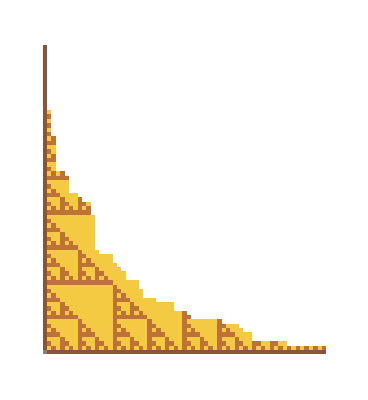

```mathematica
SimulateAssembly[SierpinskiSeed,SierpinskiTS,1000]
```

```mathematica
Dynamic[small]
```

```mathematica
(* each iteration adds 10 tiles *)
small=SierpinskiSeed;While[True,small=SimulateAssembly[small,SierpinskiTS,10]];
```

$Aborted

```mathematica
(* better: keeping track of what options there are for adding tiles, from iteration to iteration, saves time otherwise required to recalculate at each iteration *)
(* also, we take more steps between display updates, as the assembly gets larger: sqrt(n+m) tiles added for an n x m assembly *)
small=SierpinskiSeed;options={};
While[True,{small,options}=SimulateAssemblyWithOptions[small,SierpinskiTS,Round[Sqrt[Total[Dimensions[First[small]]]]],options]];
```

$Aborted

```mathematica
(* using Animate allows you to go back and replay events, if you are curious about some funny thing that happens *)
historyinfo=SimulateAssemblyHistory[SierpinskiSeed,SierpinskiTS,1000];
AnimateAssemblyHistory[historyinfo]
```

## Another simple test case: counting forever

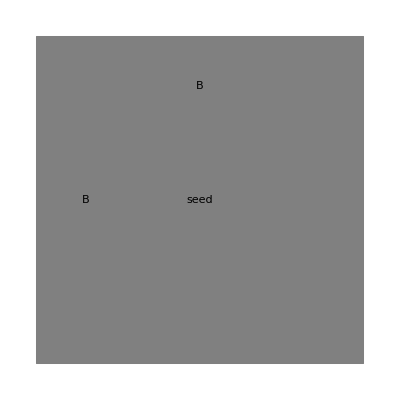
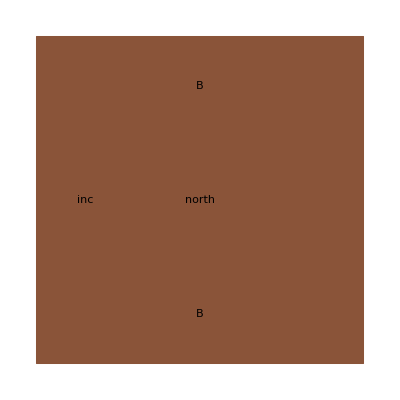
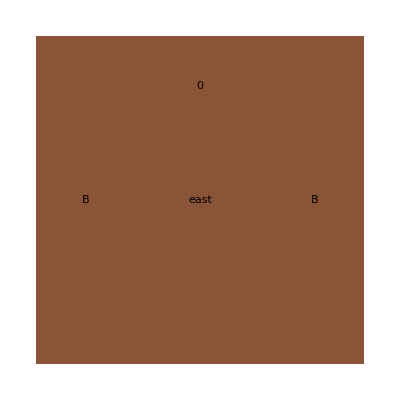
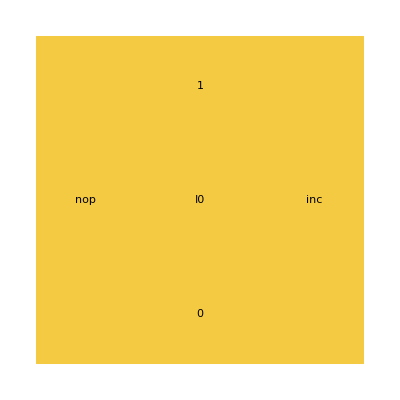
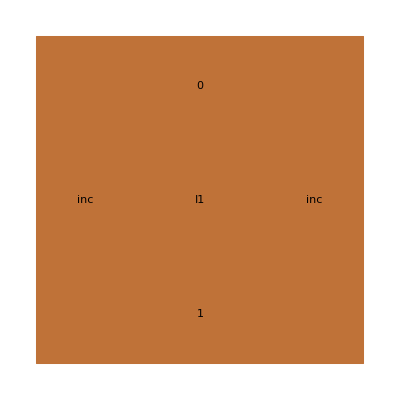
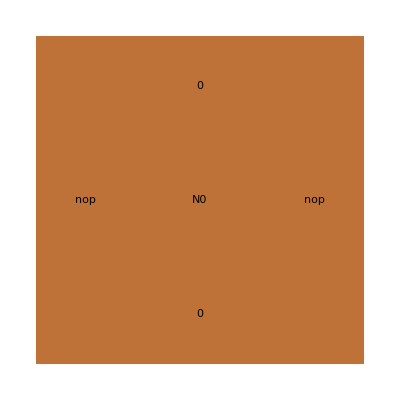
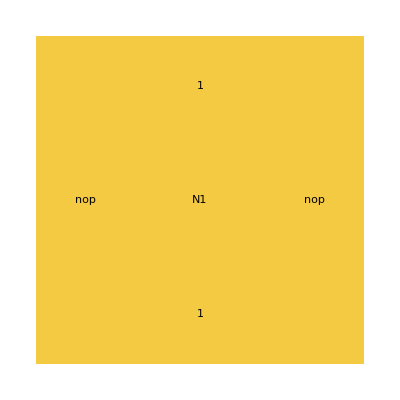

```mathematica
CountingTiles={
Tile[seed,{B,Null,Null,B},Gray],
Tile[north,{B,Null,B,inc},Blue],
Tile[east,{0,B,Null,B},Blue],
Tile[I0,{1,inc,0,nop},Green],
Tile[I1,{0,inc,1,inc},Red],
Tile[N0,{0,nop,0,nop},Red],
Tile[N1,{1,nop,1,nop},Green]
};
CountingTiles=CountingTiles/.{
Blue->ColorData["FallColors"][0.45],
Red->ColorData["FallColors"][0.65],
Green->ColorData["FallColors"][1.0]
}
```

```mathematica
Clear[CountingG]
CountingG[B]=2;
CountingG[x_Integer]=1;
CountingG[x_Symbol]=1;
CountingG[Null]=0;
CountingG[x_,y_]:=If[x===y,CountingG[x],0]
```

```mathematica
CountingTS=TileSystem[CountingTiles,2,CountingG];
CountingSeed=SeedAssembly[{{seed}},CountingTiles];
```

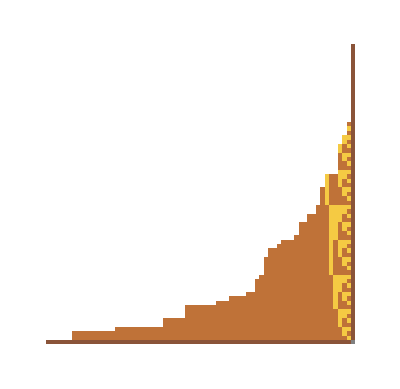

```mathematica
SimulateAssembly[CountingSeed,CountingTS,1000]
```

```mathematica
Dynamic[small]
```

```mathematica
small=CountingSeed;options={};
While[True,{small,options}=SimulateAssemblyWithOptions[small,CountingTS,Round[Sqrt[Total[Dimensions[First[small]]]]],options]];
```

$Aborted

## Tile sets for growing squares: uniquely addressed tiles, N^2 tiles

We will now explore generalized constructions for fabricating objects by molecular self-assembly.  Since tile types and bond types are named with symbols, generalized constructions will need a way to make new symbols on the fly.

```mathematica
NameIt[list__]:=ToExpression[StringJoin@@({list}/.{n_Integer:>ToString[n],v_Symbol:>ToString[v]})]
```

```mathematica
NameIt[NS,5,v,17]  (* try out functions like this, to see what they do *)
```

NS5v17

This construction makes N^2 tile types, each with unique bond types on each side, so each tile type has a unique type of neighbor on each side.

To maximize ugliness, we choose random colors for the tiles.

```mathematica
UniquelyAddressedSquareTileSet[N_]:=
Flatten[Table[
Tile[NameIt[T,i,v,j],
{NameIt[NS,i-1,v,j],NameIt[EW,i,v,j],NameIt[NS,i,v,j],NameIt[EW,i,v,j-1]}/.{v_Symbol:>Null/;Length[Flatten[StringPosition[ToString[v],"NS0"|"EW0"|"v0"]]]>0},
RGBColor@@RandomReal[1,3]],
{i,N},{j,N}],1]
Clear[UniqueSquareG]
UniqueSquareG[Null]=0;
UniqueSquareG[v_Symbol]=2;
UniqueSquareG[x_,y_]:=If[x===y,UniqueSquareG[x],0]
```

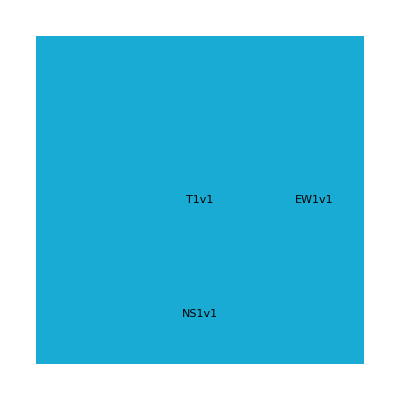
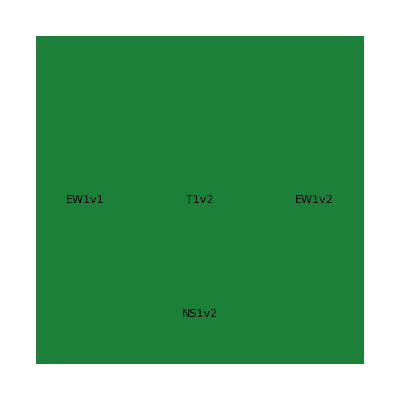
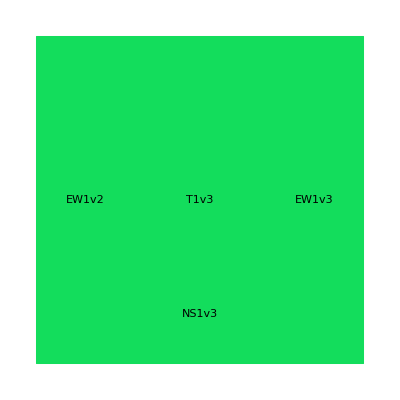
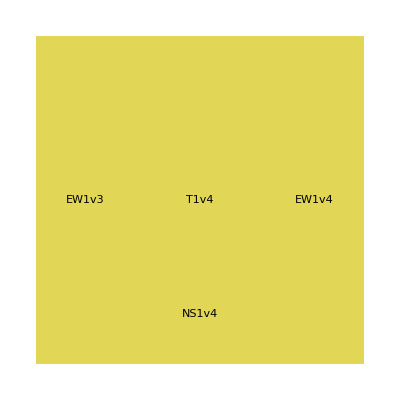
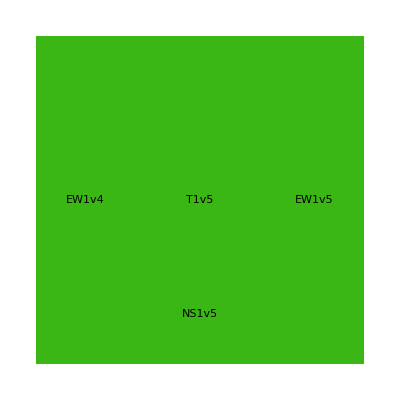
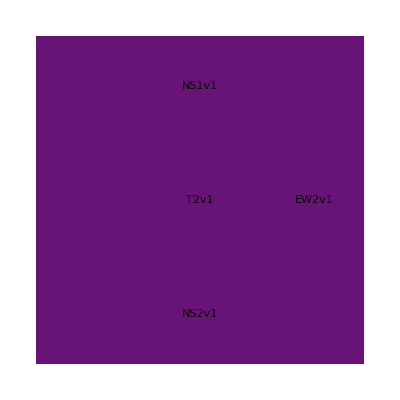
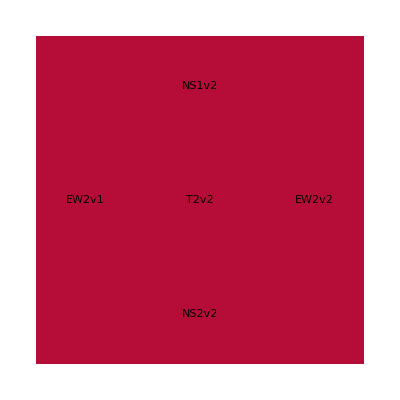
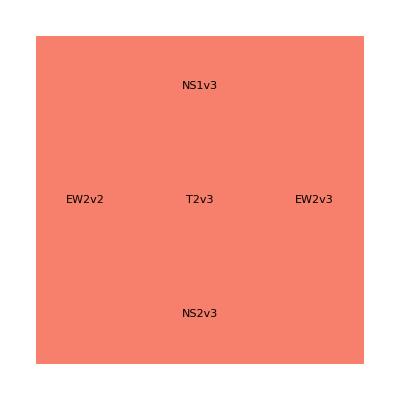

```mathematica
UniqueSquareTiles=UniquelyAddressedSquareTileSet[5]
UniqueSquareTS=TileSystem[UniqueSquareTiles,2,UniqueSquareG];
UniqueSquareSeed=SeedAssembly[{{T1v1}},UniqueSquareTiles];
```

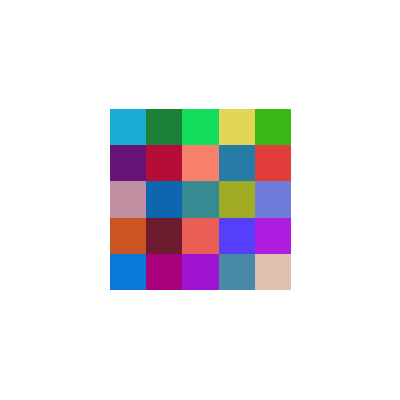

```mathematica
small=SimulateAssembly[UniqueSquareSeed,UniqueSquareTS,100]
```

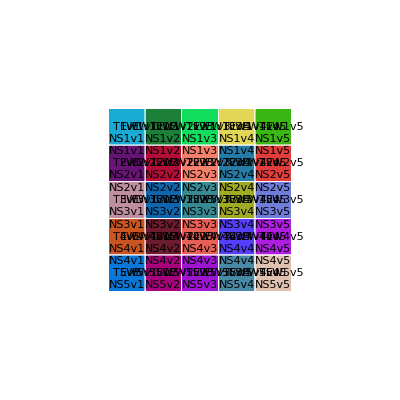

```mathematica
small//DetailForm
```

```mathematica
historyinfo=SimulateAssemblyHistory[UniqueSquareSeed,UniqueSquareTS,400];
```

```mathematica
AnimateAssemblyHistory[historyinfo]
```

```mathematica
small=UniqueSquareSeed;Dynamic[Pause[0.3];small=SimulateAssembly[small,UniqueSquareTS,1]]
```

## Tile sets for growing squares: comb-like growth, 2N-1 tiles

Fewer tile types are needed if we re-use them where we can.  Each vertical column can consist of the same uniquely-encoded tiles, while there is just one horizontal row of uniquely encoded tiles to specify the width.

```mathematica
CombSquareTileSet[N_]:=Join[
Table[
Tile[NameIt[B,j],
{Null,NameIt[EW,j],NameIt[NS,1],NameIt[EW,j-1]}/.{v_Symbol:>Null/;v===NameIt[EW,0] || v==NameIt[EW,N]},
RGBColor@@RandomReal[1,3]],
{j,N}],
Table[
Tile[NameIt[C,i],
{NameIt[NS,i-1],Null,NameIt[NS,i],Null}/.{v_Symbol:>Null/;v===NameIt[NS,N]},
RGBColor@@RandomReal[1,3]],
{i,2,N}]
]
Clear[CombSquareG]
CombSquareG[Null]=0;
CombSquareG[v_Symbol]=2;
CombSquareG[x_,y_]:=If[x===y,CombSquareG[x],0]
```

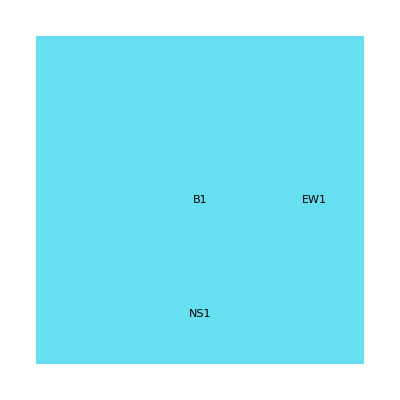
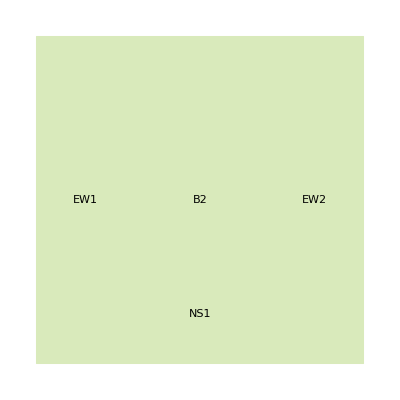
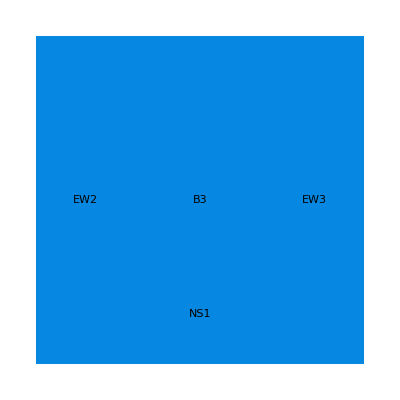
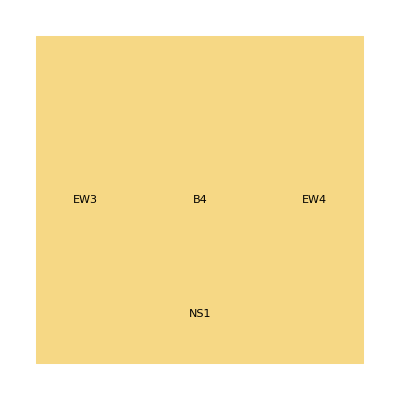
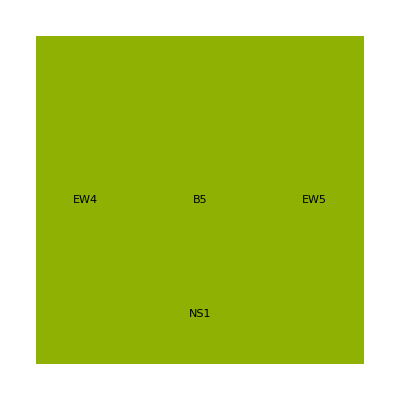
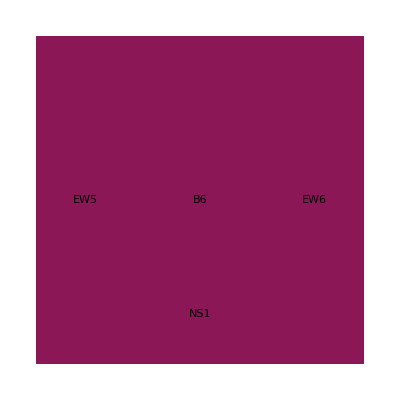
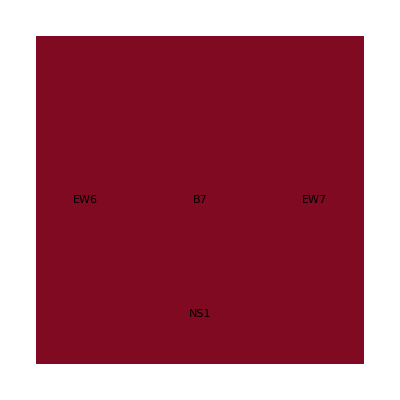
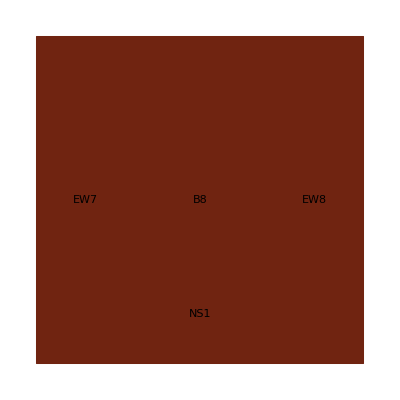

```mathematica
CombSquareTiles=CombSquareTileSet[10]
CombSquareTS=TileSystem[CombSquareTiles,2,CombSquareG];
CombSquareSeed=SeedAssembly[{{B1}},CombSquareTiles];
```

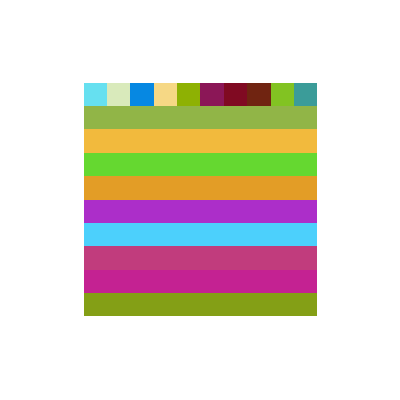

```mathematica
small=SimulateAssembly[CombSquareSeed,CombSquareTS,100]
```

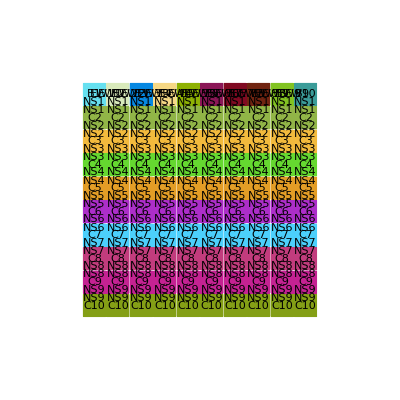

```mathematica
small//DetailForm
```

```mathematica
historyinfo=SimulateAssemblyHistory[CombSquareSeed,CombSquareTS,400];
```

```mathematica
AnimateAssemblyHistory[historyinfo]
```

```mathematica
small=CombSquareSeed;Dynamic[Pause[0.3];small=SimulateAssembly[small,CombSquareTS,1]]
```

## Tile sets for growing squares: self-delimiting diagonal, N+4 tiles

Even better:  keep the uniquely-encoded horizontal row, but use an algorithm to copy the specified with into a height of the same count.  Specifically, the algorithm is a constant number of tile types that grow a diagonal.

```mathematica
DiagonalSquareTileSet[N_]:=Join[
{Tile[B1,{Null,EW1,ll,Null},ColorData["FallColors"][1/N]],
Tile[B2,{Null,EW2,DD,EW1},ColorData["FallColors"][2/N]]},
Table[Tile[NameIt[B,j],{Null,NameIt[EW,j],ur,NameIt[EW,j-1]},ColorData["FallColors"][j/N]],{j,3,N}],
{Tile[D1,{DD,dd,ll,ll},Gray],
Tile[D2,{ur,ur,DD,dd},Lighter[Gray]],
Tile[F1,{ur,ur,ur,ur},Lighter[Blue]],
Tile[F2,{ll,ll,ll,ll},Blue]}
]
Clear[DiagonalSquareG]
DiagonalSquareG[Null]=0;
DiagonalSquareG[ll]=1;
DiagonalSquareG[ur]=1;
DiagonalSquareG[dd]=1;
DiagonalSquareG[v_Symbol]=2;
DiagonalSquareG[x_,y_]:=If[x===y,DiagonalSquareG[x],0]
```

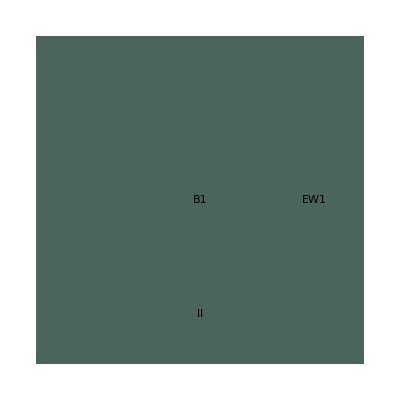
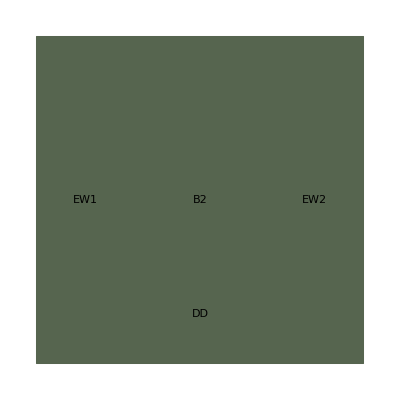
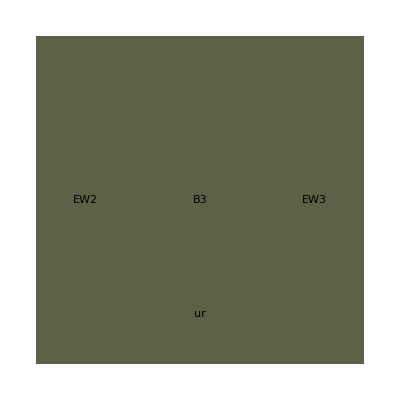
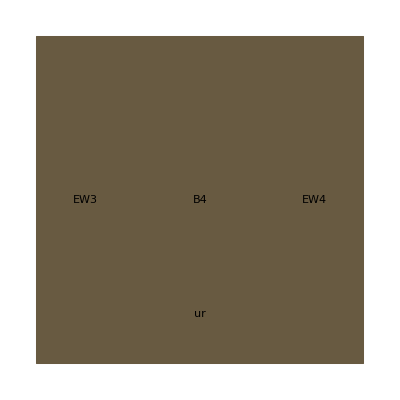
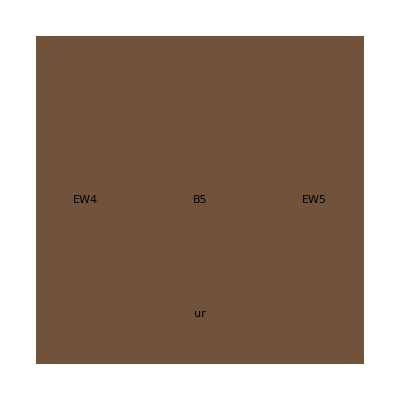
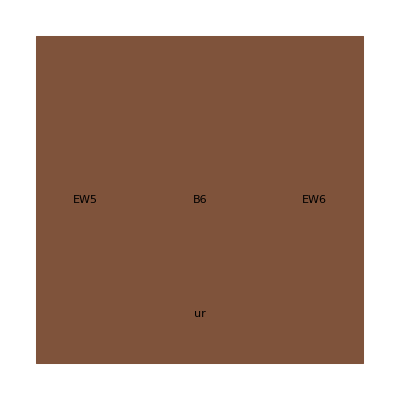
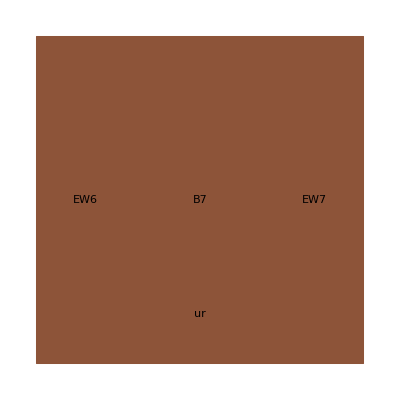
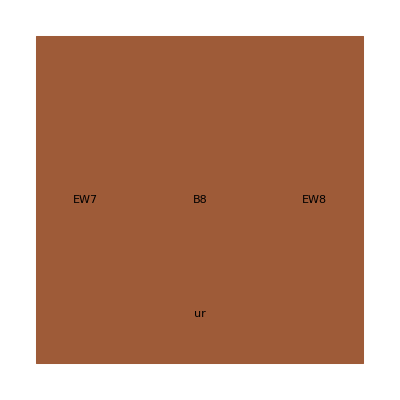

```mathematica
DiagonalSquareTiles=DiagonalSquareTileSet[15]
DiagonalSquareTS=TileSystem[DiagonalSquareTiles,2,DiagonalSquareG];
DiagonalSquareSeed=SeedAssembly[{{B1}},DiagonalSquareTiles];
```

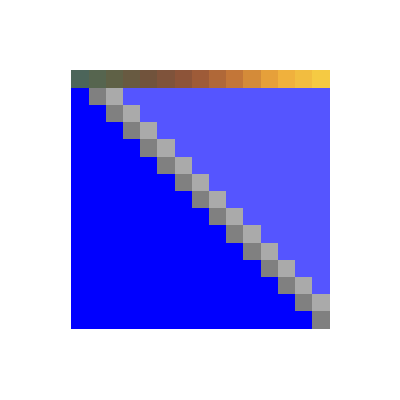

```mathematica
small=SimulateAssembly[DiagonalSquareSeed,DiagonalSquareTS,1000]
```

```mathematica
small=DiagonalSquareSeed;Dynamic[Pause[0.1];small=SimulateAssembly[small,DiagonalSquareTS,1]]
```

## Tile sets for growing squares: binary counter, O(log N) tiles

We finally obtain a near-optimal construction:  Uniquely specify a k-bit binary number, M, along the length of a uniquely-encoded horizontal strip; algorithmically grow a binary counter that counts down from M to 0 to make a O(k) x O(M) rectangle; algorithmically grow a diagonal to fill out the rectangle into a square.  To get the diagonal started in the right place, we also need to grow an O(k) x O(k) corner region, again via an algorithmic diagonal construction. To get a perfect N x N square, one must wisely chose a value of k and a value of M such that the sizes all work out.  Our somewhat lazy choices below work for N >= 8.

```mathematica
CounterSquareTileSet[N_]:=Module[{bits,k,M},
k=Ceiling[Log[2,N]];If[EvenQ[N+k],k++];
M=(N-5-k)/2; bits=IntegerDigits[M,2,k];
Join[
(* the intial row containing the binary number to start from *)
{Tile[B1,{DD,EW1,LL,DD},ColorData["FallColors"][1/(k+2)]]},
Table[Tile[NameIt[B,j],{ur,NameIt[EW,j],bits[[j-1]],NameIt[EW,j-1]},ColorData["FallColors"][j/(k+2)]],{j,2,k+1}],
{Tile[NameIt[B,k+2],{ur,Null,rr,NameIt[EW,k+1]},ColorData["FallColors"][1/(k+2)]]},
(* zig-zag logic to decrement the counter *)
{Tile[L1,{ll,nop,LL,lr},Lighter[Red]],
Tile[L2,{LL,copy,ll,lr},Red],
Tile[L3,{ll,dec,Null,lr},Darker[Red]],
Tile[R1,{rr,Null,RR,copy},Green],
Tile[R2,{RR,Null,rr,dec},Lighter[Green]],
Tile[C1,{0,copy,0,copy},Lighter[Gray]],
Tile[C2,{1,copy,1,copy},Darker[Gray]],
Tile[C3,{0,dec,1,dec},Darker[Gray]],
Tile[C4,{1,dec,0,nop},Lighter[Gray]],
Tile[C5,{0,nop,0,nop},Lighter[Gray]],
Tile[C6,{1,nop,1,nop},Darker[Gray]]},
(* big diagonal and fill-in to complete the square *)
{Tile[D1,{ul,DD,dd,ul},Gray],
Tile[D2,{dd,lr,lr,DD},Lighter[Gray]],
Tile[F1,{ul,ul,ul,ul},Lighter[Blue]],
Tile[F2,{lr,lr,lr,lr},Blue]},
(* small diagonal and fill-in to complete the corner *)
{Tile[D3,{ul,dd,DD,ul},Gray],
Tile[D4,{DD,ur,ur,dd},Lighter[Gray]],
Tile[F3,{ur,ur,ur,ur},Darker[Blue]]}
]]
Clear[CounterSquareG]
CounterSquareG[Null]=0;
CounterSquareG[v_Integer]:=1
CounterSquareG[v_Symbol]:=If[UpperCaseQ[StringTake[ToString[v],1]],2,1]
CounterSquareG[x_,y_]:=If[x===y,CounterSquareG[x],0]
```

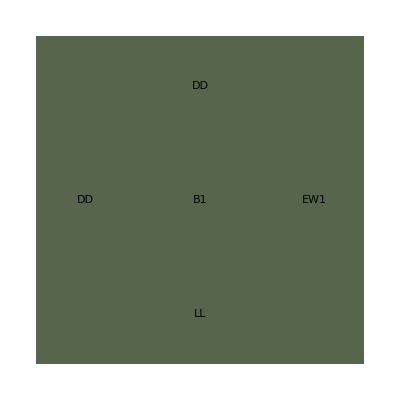
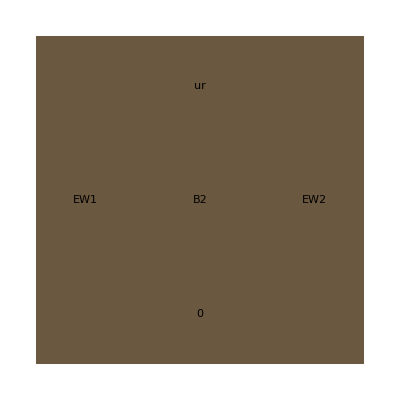
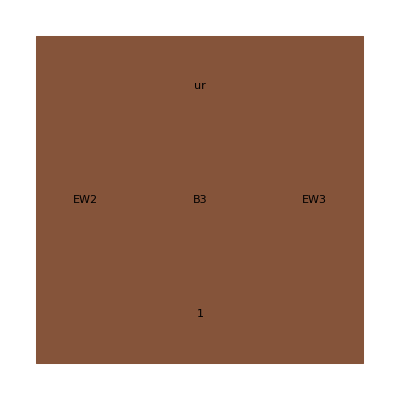
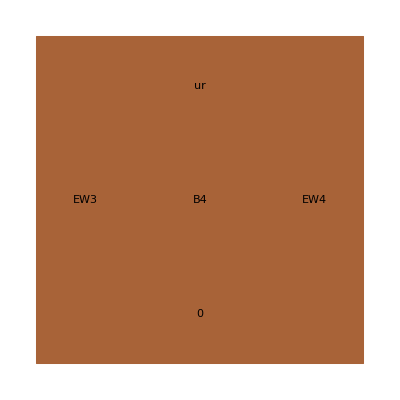
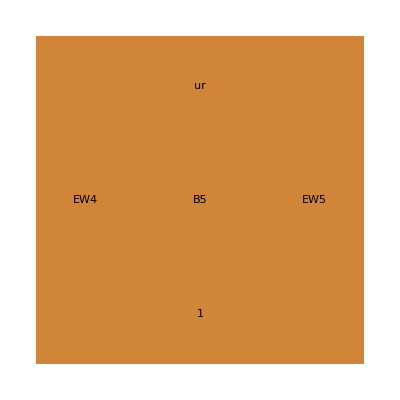
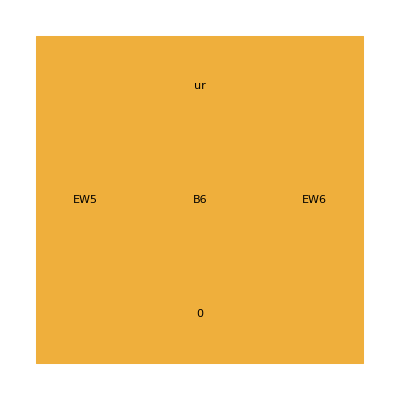
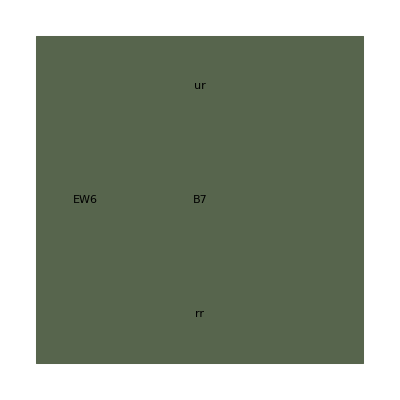
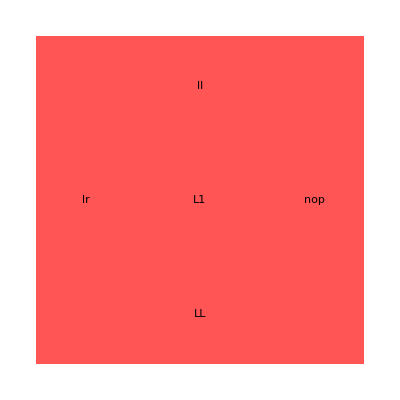

```mathematica
CounterSquareTiles=CounterSquareTileSet[30]
CounterSquareTS=TileSystem[CounterSquareTiles,2,CounterSquareG];
CounterSquareSeed=SeedAssembly[{{B1}},CounterSquareTiles];
```

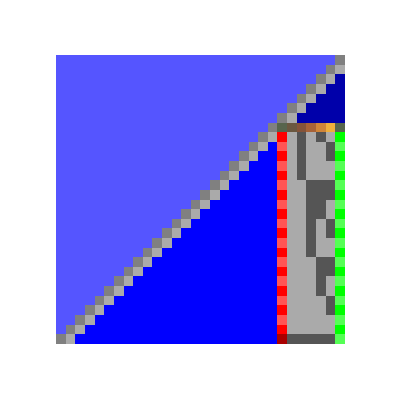

```mathematica
small=SimulateAssembly[CounterSquareSeed,CounterSquareTS,1000]
```

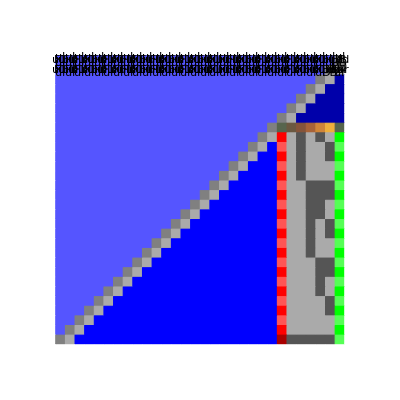

```mathematica
(* only try this for small systems, say with N < 15 *)
small//DetailForm
```

```mathematica
CounterSquareTiles=CounterSquareTileSet[99];
CounterSquareTS=TileSystem[CounterSquareTiles,2,CounterSquareG];
CounterSquareSeed=SeedAssembly[{{B1}},CounterSquareTiles];
```

```mathematica
Dynamic[small]
```

```mathematica
small=CounterSquareSeed;options={};
While[True,{small,options}=SimulateAssemblyWithOptions[small,CounterSquareTS,Round[Sqrt[Total[Dimensions[First[small]]]]],options]];
```

$Aborted

```mathematica
historyinfo=SimulateAssemblyHistory[CounterSquareSeed,CounterSquareTS,10000];
```

```mathematica
AnimateAssemblyHistory[historyinfo]
```

```mathematica
(* This demonstrates that the construction only works for N ≥ 8. *)
sizes=Table[
CounterSquareTiles=CounterSquareTileSet[N];
CounterSquareTS=TileSystem[CounterSquareTiles,2,CounterSquareG];
CounterSquareSeed=SeedAssembly[{{B1}},CounterSquareTiles];
small=SimulateAssembly[CounterSquareSeed,CounterSquareTS,1000];
With[{M=First[small]},Sum[Boole[M[[i,j]]=!=empty],{i,Length[M]},{j,Length[First[M]]}]],
{N,1,30}] //Sqrt//N
```

{5.,6.,11.,12.,13.,10.,11.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.}

## Tile sets for growing squares: N = O(TIME(TM)) using K=O(states x symbols) tile types via TMs

By simulating a Turing machine, tile assembly can grow an enormous square from just a few tile types.

Turing machines are specified by a set of state update rules of the form
	{current head state,  tape symbol being read} --> {new head state, tape symbol to write, move steps +1 or -1}
	
We demonstrate on the 2-symbol 3-state Busy Beaver TM and the 2-symbol 4-state Busy Beaver TM that maximize the number of steps taken.

```mathematica
BB3={{a,0}->{b,1,+1},{b,0}->{b,1,-1},{c,0}->{c,1,-1},{a,1}->{h,1,+1},{b,1}->{c,0,+1},{c,1}->{a,1,-1}};
```

```mathematica
TuringMachine[BB3,{a,{{},0}},20]//MatrixForm
```

({a,2,0} | {0,0,0,0,0}
{b,3,1} | {0,1,0,0,0}
{b,2,0} | {0,1,1,0,0}
{c,3,1} | {0,0,1,0,0}
{a,2,0} | {0,0,1,0,0}
{b,3,1} | {0,1,1,0,0}
{c,4,2} | {0,1,0,0,0}
{c,3,1} | {0,1,0,1,0}
{c,2,0} | {0,1,1,1,0}
{a,1,-1} | {0,1,1,1,0}
{b,2,0} | {1,1,1,1,0}
{c,3,1} | {1,0,1,1,0}
{a,2,0} | {1,0,1,1,0}
{b,3,1} | {1,1,1,1,0}
{c,4,2} | {1,1,0,1,0}
{a,3,1} | {1,1,0,1,0}
{b,4,2} | {1,1,1,1,0}
{c,5,3} | {1,1,1,0,0}
{c,4,2} | {1,1,1,0,1}
{c,3,1} | {1,1,1,1,1}
{a,2,0} | {1,1,1,1,1})

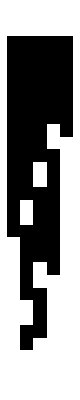

```mathematica
ArrayPlot[Last/@Reverse[TuringMachine[BB3,{a,{{},0}},25]]]
```

```mathematica
BB4 = {{a,0}->{b,1,+1},{b,0}->{a,1,-1},{c,0}->{h,1,+1},{d,0}->{d,1,+1},{a,1}->{b,1,-1},{b,1}->{c,0,-1},{c,1}->{d,1,-1},{d,1}->{a,0,+1}};
```

```mathematica
TuringMachine[BB4,{a,{{},0}},50]//MatrixForm
```

({a,5,0} | {0,0,0,0,0,0,0,0}
{b,6,1} | {0,0,0,0,1,0,0,0}
{a,5,0} | {0,0,0,0,1,1,0,0}
{b,4,-1} | {0,0,0,0,1,1,0,0}
{a,3,-2} | {0,0,0,1,1,1,0,0}
{b,4,-1} | {0,0,1,1,1,1,0,0}
{c,3,-2} | {0,0,1,0,1,1,0,0}
{d,2,-3} | {0,0,1,0,1,1,0,0}
{d,3,-2} | {0,1,1,0,1,1,0,0}
{a,4,-1} | {0,1,0,0,1,1,0,0}
{b,5,0} | {0,1,0,1,1,1,0,0}
{c,4,-1} | {0,1,0,1,0,1,0,0}
{d,3,-2} | {0,1,0,1,0,1,0,0}
{d,4,-1} | {0,1,1,1,0,1,0,0}
{a,5,0} | {0,1,1,0,0,1,0,0}
{b,6,1} | {0,1,1,0,1,1,0,0}
{c,5,0} | {0,1,1,0,1,0,0,0}
{d,4,-1} | {0,1,1,0,1,0,0,0}
{d,5,0} | {0,1,1,1,1,0,0,0}
{a,6,1} | {0,1,1,1,0,0,0,0}
{b,7,2} | {0,1,1,1,0,1,0,0}
{a,6,1} | {0,1,1,1,0,1,1,0}
{b,5,0} | {0,1,1,1,0,1,1,0}
{a,4,-1} | {0,1,1,1,1,1,1,0}
{b,3,-2} | {0,1,1,1,1,1,1,0}
{c,2,-3} | {0,1,0,1,1,1,1,0}
{d,1,-4} | {0,1,0,1,1,1,1,0}
{d,2,-3} | {1,1,0,1,1,1,1,0}
{a,3,-2} | {1,0,0,1,1,1,1,0}
{b,4,-1} | {1,0,1,1,1,1,1,0}
{c,3,-2} | {1,0,1,0,1,1,1,0}
{d,2,-3} | {1,0,1,0,1,1,1,0}
{d,3,-2} | {1,1,1,0,1,1,1,0}
{a,4,-1} | {1,1,0,0,1,1,1,0}
{b,5,0} | {1,1,0,1,1,1,1,0}
{c,4,-1} | {1,1,0,1,0,1,1,0}
{d,3,-2} | {1,1,0,1,0,1,1,0}
{d,4,-1} | {1,1,1,1,0,1,1,0}
{a,5,0} | {1,1,1,0,0,1,1,0}
{b,6,1} | {1,1,1,0,1,1,1,0}
{c,5,0} | {1,1,1,0,1,0,1,0}
{d,4,-1} | {1,1,1,0,1,0,1,0}
{d,5,0} | {1,1,1,1,1,0,1,0}
{a,6,1} | {1,1,1,1,0,0,1,0}
{b,7,2} | {1,1,1,1,0,1,1,0}
{c,6,1} | {1,1,1,1,0,1,0,0}
{d,5,0} | {1,1,1,1,0,1,0,0}
{d,6,1} | {1,1,1,1,1,1,0,0}
{a,7,2} | {1,1,1,1,1,0,0,0}
{b,8,3} | {1,1,1,1,1,0,1,0}
{a,7,2} | {1,1,1,1,1,0,1,1})

```mathematica
ArrayPlot[Last/@Reverse[TuringMachine[BB4,{a,{{},0}},110]]]
```

-Graphics-

Now we can convert a Turing machine into a tile set. For each symbol, we have two tile types: one for copying it to the left of the head, one for copying it to the right of the head.  For each Turing machine rule, we have four tile types: one for reading a new cell when coming from the left, one for reading a new cell when coming from the right, one used just for setting up initial seeds, and one for starting a new layer while writing the new symbol in the cell’s site.

Note that Mathematical allows special characters in symbol names, for example here we use \ [ CapitalDelta ] which if typed without the spaces will become the Greek character.

```mathematica
TuringMachineTiles[TM_]:=Module[{symbols,states, haltstates,readingtiles,writingtiles,haltingtiles},
states=Union[First[First[#]]&/@TM];  (* head states that are acted on, i.e. not including halt state *)
symbols=Union[Last[First[#]]&/@TM,Last[#][[2]]&/@TM]; (* symbols either read or written *)
readingtiles[{head_,symbol_}->{newhead_,newsymbol_,_}]:={
Tile[NameIt[head,symbol,L],{NameIt[head,Δ,symbol],head,symbol,LEFT},
ColorData["DeepSeaColors"][First[Flatten[Position[states,head]]]/Length[states]]],
Tile[NameIt[head,symbol,R],{NameIt[head,Δ,symbol],RIGHT,symbol,head},
ColorData["DeepSeaColors"][First[Flatten[Position[states,head]]]/Length[states]]],
Tile[NameIt[head,symbol],{NameIt[head,Δ,symbol],RIGHT,symbol,LEFT},
ColorData["DeepSeaColors"][First[Flatten[Position[states,head]]]/Length[states]]] (* this tile is used only for setting up input *)
};
writingtiles[{head_,symbol_}->{newhead_,newsymbol_,+1}]:={
Tile[NameIt[head,Δ,symbol,R],{newsymbol,If[MemberQ[states,newhead],newhead,RIGHT],NameIt[head,Δ,symbol],LEFT},
ColorData["DeepSeaColors"][First[Flatten[Position[states,head]]]/Length[states]]]
};
writingtiles[{head_,symbol_}->{newhead_,newsymbol_,-1}]:={
Tile[NameIt[head,Δ,symbol,L],{newsymbol,RIGHT,NameIt[head,Δ,symbol],If[MemberQ[states,newhead],newhead,LEFT]},
ColorData["DeepSeaColors"][First[Flatten[Position[states,head]]]/Length[states]]]
};
Join[
Table[Tile[NameIt[C,s,L],{s,LEFT,s,LEFT},ColorData["FallColors"][First[Flatten[Position[symbols,s]]]/Length[symbols]]],{s,symbols}],
Table[Tile[NameIt[C,s,R],{s,RIGHT,s,RIGHT},ColorData["FallColors"][First[Flatten[Position[symbols,s]]]/Length[symbols]]],{s,symbols}],
Flatten[readingtiles/@TM,2],
Flatten[writingtiles/@TM,2]
]
]
Clear[TuringG]
TuringG[Null]=0;
TuringG[v_]:=If[StringMatchQ[ToString[v],"*Δ*"],2,1]
TuringG[x_,y_]:=If[x===y,TuringG[x],0]
```

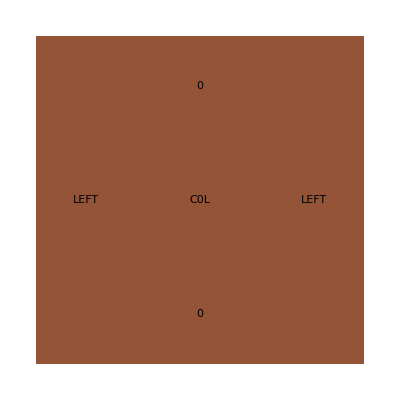
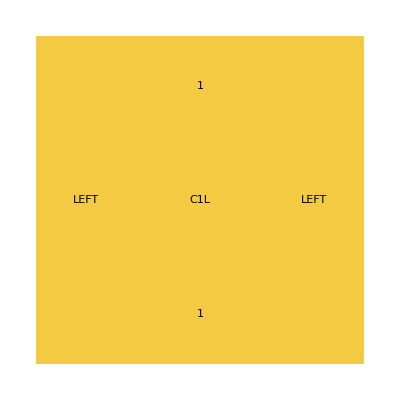
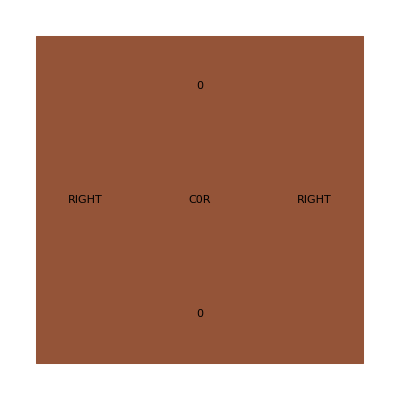
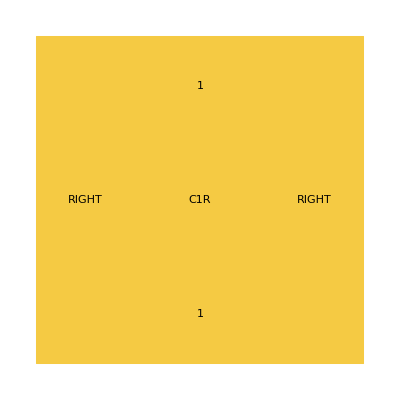
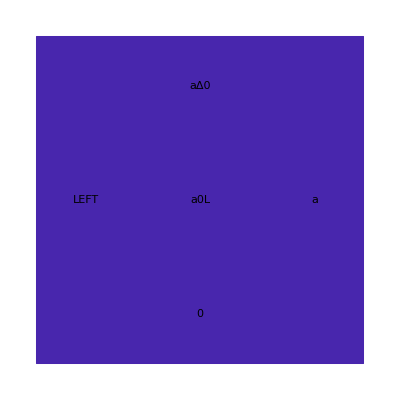
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TuringMachineTiles[BB3]
```

```mathematica
TuringTestTiles=TuringMachineTiles[BB3]; (* also try BB4 *)
TuringTestTS=TileSystem[TuringTestTiles,2,TuringG];
TuringTestSeed=SeedAssembly[{{C0L,C0L,C0L,C0L,C0L,C0L,C0L,C0L,C0L,C0L,C0L,C0L,a0,C0R,C0R,C0R,C0R,C0R,C0R,C0R},Table[C0L,20]},TuringTestTiles]
```

-Graphics-

```mathematica
small=TuringTestSeed;Dynamic[Pause[0.1];small=SimulateAssembly[small,TuringTestTS,1]]
```

```mathematica
TuringTestSeed//DetailForm
```

-Graphics-

```mathematica
small=SimulateAssembly[TuringTestSeed,TuringTestTS,1000]; small//DetailForm
```

-Graphics-

```mathematica
historyinfo=SimulateAssemblyHistory[TuringTestSeed,TuringTestTS,50000];
AnimateAssemblyHistory[historyinfo]
```

We now combine four oriented copies of the Turing machine tiles, to create a square that stops growing when the Turing machines halt.  In addition to the four rotated Turing machine tile sets, we need a seed tile, the tiles that stick to the four sides of the seed and contain the initial state & symbol of the Turing machine, and four diagonal tiles that provide a seam between the four rotated executions of the Turing machine.  Note that we are considering a Turing machine that conceptually starts on a uniform “blank” tape with just the give symbol initially.

```mathematica
RotateTile[N,Tile[ID_,{n_,e_,s_,w_},color_]]:=Tile[NameIt[N,ID],{NameIt[N,n],NameIt[N,e],NameIt[N,s],NameIt[N,w]},color]
RotateTile[E,Tile[ID_,{n_,e_,s_,w_},color_]]:=Tile[NameIt[E,ID],{NameIt[E,w],NameIt[E,n],NameIt[E,e],NameIt[E,s]},color]
RotateTile[S,Tile[ID_,{n_,e_,s_,w_},color_]]:=Tile[NameIt[S,ID],{NameIt[S,s],NameIt[S,w],NameIt[S,n],NameIt[S,e]},color]
RotateTile[W,Tile[ID_,{n_,e_,s_,w_},color_]]:=Tile[NameIt[W,ID],{NameIt[W,e],NameIt[W,s],NameIt[W,w],NameIt[W,n]},color]
RotateTiles[tileset_]:=Join[RotateTile[N,#]&/@tileset,RotateTile[E,#]&/@tileset,RotateTile[S,#]&/@tileset,RotateTile[W,#]&/@tileset]
```

```mathematica
TuringSquareTileSet[TM_,state_,symbol_]:=Join[
RotateTiles[TuringMachineTiles[TM]],
{Tile[seed,{NΔ,EΔ,SΔ,WΔ},Gray],
Tile[north,{NameIt[N,state,Δ,symbol],NRIGHT,NΔ,NLEFT},Gray],
Tile[east,{ELEFT,NameIt[E,state,Δ,symbol],ERIGHT,EΔ},Gray],
Tile[south,{SΔ,SLEFT,NameIt[S,state,Δ,symbol],NameIt[S,RIGHT]},Gray],
Tile[west,{WRIGHT,WΔ,WLEFT,NameIt[W,state,Δ,symbol]},Gray],
Tile[D1,{NameIt[N,symbol],NameIt[E,symbol],ELEFT,NRIGHT},Gray],
Tile[D2,{ERIGHT,NameIt[E,symbol],NameIt[S,symbol],SLEFT},Gray],
Tile[D3,{WLEFT,SRIGHT,NameIt[S,symbol],NameIt[W,symbol]},Gray],
Tile[D4,{NameIt[N,symbol],NLEFT,WRIGHT,NameIt[W,symbol]},Gray]
}]
```

```mathematica
TuringSquareTiles=TuringSquareTileSet[BB3,a,0]; (* try BB4 also, but be prepared to wait... *)
TuringSquareTS=TileSystem[TuringSquareTiles,2,TuringG];
TuringSquareSeed=SeedAssembly[{{seed}},TuringSquareTiles];
```

```mathematica
TuringSquareTiles
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
small=SimulateAssembly[TuringSquareSeed,TuringSquareTS,50000]
```

SimulateAssembly[SeedAssembly[{{seed}},TuringSquareTileSet[{{a,0}→{b,1,1},{b,0}→{b,1,-1},{c,0}→{c,1,-1},{a,1}→{h,1,1},{b,1}→{c,0,1},{c,1}→{a,1,-1}},a,0]],TileSystem[tiles...,T=2, G],50000]

```mathematica
historyinfo=SimulateAssemblyHistory[TuringSquareSeed,TuringSquareTS,10000];
AnimateAssemblyHistory[historyinfo]
```

```mathematica
Dynamic[small]
```

```mathematica
small=TuringSquareSeed;options={};
While[True,{small,options}=SimulateAssemblyWithOptions[small,TuringSquareTS,Round[Sqrt[Total[Dimensions[First[small]]]]],options]];
```

$Aborted

## Examining self-healing and tile-set transformations

First we review the Sierpinski tile set, remind ourselves how it grows, and show that although it grows back after being punctured, there are permanent wound defects.  Be sure to first run the code in the Sierpinski tile set section above.

```mathematica
SierpinskiTiles
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Dynamic[(AssemblyGraphics/@{small,smallp})/.Graphics[a___]:>Graphics[a,ImageSize->Large]]
```

```mathematica
small=SierpinskiSeed;options={};smallp=SierpinskiSeed;optionsp={};
While[True,
{small,options}=SimulateAssemblyWithOptions[small,SierpinskiTS,30,options];
{smallp,optionsp}=SimulatePuncturedAssemblyHistory[smallp,SierpinskiTS,30,BlastRate->0.1,BlastSize->6,PreserveBoundary->3,KeepHistory->False,GrowthOptions->optionsp]
];
```

$Aborted

```mathematica
historyinfo=SimulatePuncturedAssemblyHistory[SierpinskiSeed,SierpinskiTS,3000,BlastRate->0.05,BlastSize->6,PreserveBoundary->3];
```

```mathematica
AnimateAssemblyHistory[historyinfo]
```

Now we will use a self-healing transformation where each tile of the original system (which can attach in multiple directions, despite each being used only in one intended growth direction during normal growth) becomes nine tiles (which as a block will only grow in the intended direction, and which occasionally share the same tile in different blocks).

Here, we only specific the transformation for rule tiles that have inputs on their west and south sides, and outputs on their north and east sides, and thus grow in a north-east direction.  The boundary tiles and seed tiles are similarly oriented.  Thus, this transformation would need to be modified and reoriented before it could be applied to the infinite-growth binary counting tile set.  For tile sets that use tiles that grow with different types of input patterns (e.g. two opposite sides) there are more complex transformations that use larger block sizes, e.g. 7x7 instead of 3x3.

Make sure that the function NameIt[ ] is defined, as given above for the square tile sets.

```mathematica
Clear[SelfHealing]
SelfHealing[Tile[ID_,{n_,e_,s_,w_},color_],G_,NorthEast]:={
Tile[NameIt["t",ID,1],{NameIt["t",ID,1],NameIt["t",ID,1],NameIt["b",s,1],NameIt["b",w,1]},color],
Tile[NameIt["t",ID,2],{NameIt["t",ID,3],NameIt["t",ID,2],NameIt["b",s,2],NameIt["t",ID,1]},color],
Tile[NameIt["t",ID,3],{NameIt["t",ID,2],NameIt["t",ID,3],NameIt["t",ID,1],NameIt["b",w,2]},color],
Tile[NameIt["t",ID,4],{NameIt["b",n,1],NameIt["t",ID,4],NameIt["t",ID,2],Null},color],
Tile[NameIt["t",ID,5],{NameIt["T",ID,5],NameIt["T",ID,5],NameIt["t",ID,3],NameIt["t",ID,3]},color],
Tile[NameIt["t",ID,6],{NameIt["t",ID,4],NameIt["b",e,1],Null,NameIt["t",ID,2]},color],
Tile[NameIt["t",ID,7],{NameIt["b",n,2],NameIt["t",ID,6],NameIt["T",ID,5],NameIt["t",ID,4]},color],
Tile[NameIt["t",ID,8],{NameIt["t",ID,6],NameIt["b",e,2],NameIt["t",ID,4],NameIt["T",ID,5]},color],
Tile[NameIt["t",ID,9],{Null,Null,NameIt["t",ID,6],NameIt["t",ID,6]},color]
} /; G/@{n,e,s,w}==={1,1,1,1}
SelfHealing[Tile[ID_,{n_,e_,s_,w_},color_],G_,NorthEast]:={
Tile[NameIt["t",ID,1],{NameIt["T",ID,1],NameIt["t",ID,1],Null,NameIt["B",w,1]},color],
Tile[NameIt["t",ID,2],{NameIt["t",ID,3],NameIt["b",e,5],Null,NameIt["t",ID,1]},color],
Tile[NameIt["t",ID,3],{NameIt["t",ID,2],NameIt["t",ID,3],NameIt["T",ID,1],Null},color],
Tile[NameIt["t",ID,4],{NameIt["b",n,1],NameIt["T",ID,4],NameIt["t",ID,2],NameIt["b",w,3]},color],
Tile[NameIt["t",ID,5],{NameIt["t",ID,5],NameIt["T",ID,5],NameIt["t",ID,3],NameIt["t",ID,3]},color],
Tile[NameIt["b",e,0],{NameIt["b",e,4],NameIt["B",e,1],Null,NameIt["b",e,5]},Darker[White]], (* this tile may be shared across original tile blocks *)
Tile[NameIt["t",ID,7],{NameIt["b",n,2],NameIt["t",ID,6],NameIt["t",ID,5],NameIt["T",ID,4]},color],
Tile[NameIt["t",ID,8],{NameIt["t",ID,6],Null,NameIt["b",e,4],NameIt["T",ID,5]},color],
Tile[NameIt["t",ID,9],{Null, NameIt["b",e,3],NameIt["t",ID,6],NameIt["t",ID,6]},color]
} /; G/@{n,e,s,w}==={1,2,0,2}
SelfHealing[Tile[ID_,{n_,e_,s_,w_},color_],G_,NorthEast]:={
Tile[NameIt["t",ID,1],{NameIt["t",ID,1],NameIt["T",ID,1],NameIt["B",s,1],Null},color],
Tile[NameIt["t",ID,2],{NameIt["t",ID,3],NameIt["t",ID,2],Null,NameIt["T",ID,1]},color],
Tile[NameIt["t",ID,3],{NameIt["b",n,5],NameIt["t",ID,3],NameIt["t",ID,1],Null},color],
Tile[NameIt["b",n,1],{NameIt["B",n,1],NameIt["b",n,4],NameIt["b",n,5],Null},Darker[White]], (* this tile may be shared across original tile blocks *)
Tile[NameIt["t",ID,5],{NameIt["T",ID,5],NameIt["t",ID,5],NameIt["t",ID,3],NameIt["t",ID,3]},color],
Tile[NameIt["t",ID,6],{NameIt["T",ID,4],NameIt["b",e,1],NameIt["b",s,3],NameIt["t",ID,2]},color],
Tile[NameIt["t",ID,7],{Null,NameIt["t",ID,6],NameIt["T",ID,5],NameIt["b",n,4]},color],
Tile[NameIt["t",ID,8],{NameIt["t",ID,6],NameIt["b",e,2],NameIt["T",ID,4],NameIt["t",ID,5]},color],
Tile[NameIt["t",ID,9],{NameIt["b",n,3],Null,NameIt["t",ID,6],NameIt["t",ID,6]},color]
} /; G/@{n,e,s,w}==={2,1,2,0}
SelfHealing[Tile[ID:seed,{n_,e_,s_,w_},color_],G_,NorthEast]:={
Tile[NameIt["t",ID,1],{NameIt["t",ID,1],NameIt["t",ID,1],Null,Null},color],
Tile[NameIt["t",ID,2],{NameIt["T",ID,3],NameIt["b",e,5],Null,NameIt["t",ID,1]},color],
Tile[NameIt["t",ID,3],{NameIt["b",n,5],NameIt["T",ID,3],NameIt["t",ID,1],Null},color],
Tile[NameIt["b",n,1],{NameIt["B",n,1],NameIt["b",n,4],NameIt["b",n,5],Null},Darker[White]], (* this tile may be shared across original tile blocks *)
Tile[ID,{NameIt["T",ID,4],NameIt["T",ID,4],NameIt["T",ID,3],NameIt["T",ID,3]},color],
Tile[NameIt["b",e,0],{NameIt["b",e,4],NameIt["B",e,1],Null,NameIt["b",e,5]},Darker[White]], (* this tile may be shared across original tile blocks *)
Tile[NameIt["t",ID,7],{Null,NameIt["t",ID,2],NameIt["T",ID,4],NameIt["b",n,4]},color],
Tile[NameIt["t",ID,8],{NameIt["t",ID,2],Null,NameIt["b",e,4],NameIt["T",ID,4]},color],
Tile[NameIt["t",ID,9],{NameIt["b",n,3],NameIt["b",e,3],NameIt["t",ID,2],NameIt["t",ID,2]},color]
} /; G/@{n,e,s,w}==={2,2,0,0}
SelfHealing[TileSystem[tiles_,2,G_],NorthEast]:=TileSystem[
Union@@(SelfHealing[#,G,NorthEast]&/@tiles),
2,
SelfHealingG
]
Clear[SelfHealingG]
SelfHealingG[Null]=0;
SelfHealingG[v_Symbol]:=If[UpperCaseQ[StringTake[ToString[v],1]],2,1]
SelfHealingG[x_,y_]:=If[x===y,SelfHealingG[x],0]
```

```mathematica
SHSierpinskiTS=SelfHealing[SierpinskiTS,NorthEast];
```

```mathematica
(* what does the transformed tile set look like? *)
First[SHSierpinskiTS]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SHSierpinskiSeed=SeedAssembly[{{seed}},First[SHSierpinskiTS]];
```

```mathematica
SimulateAssembly[SHSierpinskiSeed,SHSierpinskiTS,40]//DetailForm
```

-Graphics-

```mathematica
historyinfo=SimulateAssemblyHistory[SHSierpinskiSeed,SHSierpinskiTS,400];
```

```mathematica
AnimateAssemblyHistory[historyinfo]
```

```mathematica
Dynamic[smallh]
```

```mathematica
smallh=SHSierpinskiSeed;optionsh={};
While[True,
{smallh,optionsh}=SimulatePuncturedAssemblyHistory[smallh,SHSierpinskiTS,10,BlastRate->0.02,BlastSize->9,PreserveBoundary->3,KeepHistory->False,GrowthOptions->optionsh]
];
```

$Aborted

```mathematica
Dynamic[(AssemblyGraphics/@{small,smallp,smallh})/.Graphics[a___]:>Graphics[a,ImageSize->Medium]]
```

```mathematica
small=SierpinskiSeed;options={};smallp=SierpinskiSeed;optionsp={};smallh=SHSierpinskiSeed;optionsh={};
While[True,
{small,options}=SimulateAssemblyWithOptions[small,SierpinskiTS,10,options];
{smallp,optionsp}=SimulatePuncturedAssemblyHistory[smallp,SierpinskiTS,10,BlastRate->0.18,BlastSize->3,PreserveBoundary->3,KeepHistory->False,GrowthOptions->optionsp];
{smallh,optionsh}=SimulatePuncturedAssemblyHistory[smallh,SHSierpinskiTS,90,BlastRate->0.02,BlastSize->9,PreserveBoundary->3,KeepHistory->False,GrowthOptions->optionsh]
];
```

$Aborted

```mathematica
historyinfo=SimulatePuncturedAssemblyHistory[SHSierpinskiSeed,SHSierpinskiTS,8000,BlastRate->0.05,BlastSize->6,PreserveBoundary->3];
```

```mathematica
AnimateAssemblyHistory[historyinfo]
```

### Some relevant references

Rothemund, Paul WK, and Erik Winfree. “The program-size complexity of self-assembled squares.” In Proceedings of the thirty-second annual ACM symposium on Theory of computing, pp. 459-468. 2000.
Adleman, Leonard, Qi Cheng, Ashish Goel, and Ming-Deh Huang. “Running time and program size for self-assembled squares.” In Proceedings of the thirty-third annual ACM symposium on Theory of computing, pp. 740-748. 2001.
Winfree, Erik, and Renat Bekbolatov. “Proofreading tile sets: Error correction for algorithmic self-assembly.” In International Workshop on DNA-Based Computers, pp. 126-144. Springer, Berlin, Heidelberg, 2003.
Winfree, Erik.  “Self-healing tile sets.” in Nanotechnology: science and computation, pp 55-78.  Springer, Berlin, Heidelberg, 2006.
Aggarwal, Gagan, Qi Cheng, Michael H. Goldwasser, Ming-Yang Kao, Pablo Moisset De Espanes, and Robert T. Schweller. “Complexities for generalized models of self-assembly.” SIAM Journal on Computing 34, no. 6 (2005): 1493-1515.
Soloveichik, David, and Erik Winfree. “Complexity of self-assembled shapes.” SIAM Journal on Computing 36, no. 6 (2007): 1544-1569.
Doty, David. “Theory of algorithmic self-assembly.” Communications of the ACM 55, no. 12 (2012): 78-88.